# Tutorial notebook

CmdStan package

```mathematica
<<CmdStan`
```

```mathematica
?CmdStan`*
```

A boolean option to define verbosity.

Stan code

```mathematica
SetDirectory[$TemporaryDirectory]
```

/tmp

```mathematica
stanCode="data
{
  int<lower = 0> N;
  vector[N] x;
  vector[N] y;
}
parameters
{
  real alpha;
  real beta;
  real<lower = 0> sigma;
}
model {
  y ~normal(alpha + beta * x, sigma);
}";
```

```mathematica
stanCodeFile=ExportStanCode["linear_regression.stan",stanCode]
```

/tmp/linear_regression.stan

Stan exe

```mathematica
stanExeFile = CompileStanCode[stanCodeFile,StanVerbose->False]
```

/tmp/linear_regression

Linear regression data

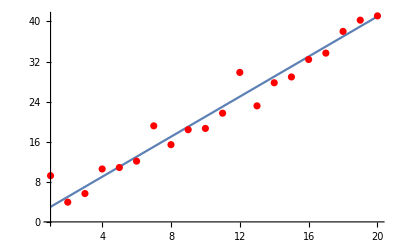

```mathematica
σ=3;α=1;β=2;
n=20;
X=Range[n];
Y=α+β*X+RandomVariate[NormalDistribution[0,σ],n];
Show[Plot[α+β*x,{x,Min[X],Max[X]}],ListPlot[Transpose@{X,Y},PlotStyle->Red]]
```

```mathematica
Export["~/GitHub/MathematicaStan/figures/linRegData.png",%]
```

~/GitHub/MathematicaStan/figures/linRegData.png

Stan data.R file

```mathematica
stanData=<|"N"->n,"x"->X,"y"->Y|>;
stanDataFile=ExportStanData[stanExeFile,stanData]
```

/tmp/linear_regression.data.R

Run Stan: “method=Optimize”

```mathematica
stanResultFile=RunStan[stanExeFile,OptimizeDefaultOptions]
```

Running: /tmp/linear_regression method=optimize data file=/tmp/linear_regression.data.R output file=/tmp/linear_regression.csv

method = optimize
  optimize
    algorithm = lbfgs (Default)
      lbfgs
        init_alpha = 0.001 (Default)
        tol_obj = 9.9999999999999998e-13 (Default)
        tol_rel_obj = 10000 (Default)
        tol_grad = 1e-08 (Default)
        tol_rel_grad = 10000000 (Default)
        tol_param = 1e-08 (Default)
        history_size = 5 (Default)
    iter = 2000 (Default)
    save_iterations = 0 (Default)
id = 0 (Default)
data
  file = /tmp/linear_regression.data.R
init = 2 (Default)
random
  seed = 2786475854
output
  file = /tmp/linear_regression.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)

Initial log joint probability = -817.041
    Iter      log prob        ||dx||      ||grad||       alpha      alpha0  # evals  Notes 
      25      -27.4891   0.000322531    0.00243263           1           1       39   
Optimization terminated normally: 
  Convergence detected: relative gradient magnitude is below tolerance

/tmp/linear_regression.csv

```mathematica
RunStan[stanExeFile,OptimizeDefaultOptions,StanVerbose->False]
```

/tmp/linear_regression.csv

```mathematica
OptimizeDefaultOptions
```

method=optimize

Load result

```mathematica
stanResult=ImportStanResult[stanResultFile]
```

file: /tmp/linear_regression.csv
metaData: lp__ 
    data: alpha , beta , sigma

```mathematica
GetStanResultMetaData[stanResult,"lp__"]
αe=GetStanResult[stanResult,"alpha"]
βe=GetStanResult[stanResult,"beta"]
σe=GetStanResult[stanResult,"sigma"]
```

{-27.4891}

{2.03831}

{1.90526}

{2.39756}

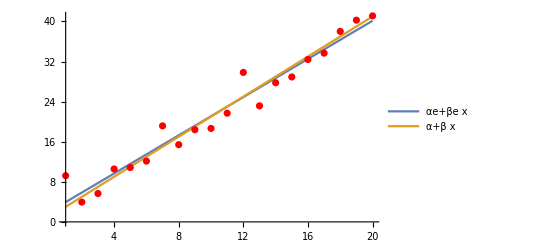

~/GitHub/MathematicaStan/figures/linRegEstimate.png

```mathematica
Show[Plot[{αe+βe*x,α+β*x},{x,Min[X],Max[X]},PlotLegends->"Expressions"],ListPlot[Transpose@{X,Y},PlotStyle->Red]]
Export["~/GitHub/MathematicaStan/figures/linRegEstimate.png",%]
```

Run Stan: “method=Variational”

```mathematica
myOpt=VariationalDefaultOptions
```

method=variational

```mathematica
myOpt=SetStanOption[myOpt,"output.file",FileNameJoin[{Directory[],"myOutputFile.csv"}]]
```

method=variational adapt output file=/tmp/myOutputFile.csv

```mathematica
myOpt=SetStanOption[myOpt,"method.adapt.iter",123]
```

method=variational adapt iter=123 output file=/tmp/myOutputFile.csv

```mathematica
GetStanOption[myOpt,"method.adapt.iter"]
```

123

```mathematica
myOpt=RemoveStanOption[myOpt,"method.adapt.iter"]
```

method=variational output file=/tmp/myOutputFile.csv

```mathematica
myOutputFile=RunStan[stanExeFile,myOpt,StanVerbose->False]
```

/tmp/myOutputFile.csv

```mathematica
myResult=ImportStanResult[myOutputFile]
```

file: /tmp/myOutputFile.csv
metaData: lp__ , log_p__ , log_g__ 
    data: alpha , beta , sigma

```mathematica
GetStanResult[myResult,"alpha"]
```

2.0353

0.317084

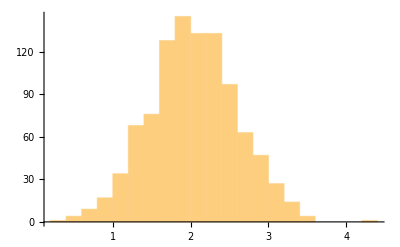

```mathematica
MapStanResult[Mean,myResult,"alpha"]
MapStanResult[Variance,myResult,"alpha"]
MapStanResult[Histogram,myResult,"alpha"]
```

```mathematica
Export["~/GitHub/MathematicaStan/figures/linRegHisto.png",%]
```

~/GitHub/MathematicaStan/figures/linRegHisto.png

```mathematica
E
```

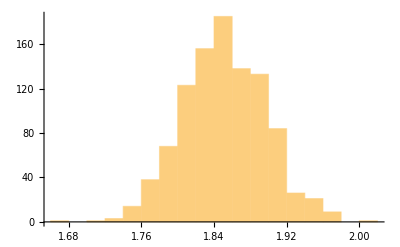

```mathematica
MapStanResult[Histogram,myResult,"beta"]
```

```mathematica
?MapStanResult
```

MapStanResult[(f_Function|f_Symbol),result_StanResult,varName_String] maps f to each component of the varName variable. Examples: f=Mean, Variance, ... or Histogram